### From hep - ph/9603205 (Appendix A1): x = (m_S/(2 m_Q))^2

```mathematica
nmax=3;
```

```mathematica
fLight[x_]=3/2 Normal[Series[z(1+(1-z)ArcSin[1/(√z)]^2)/.{z->1/x},{x,0,nmax}]];
fHeavy[x_]=FullSimplify[3/2 Normal[Series[z(1+(1-z)(-1/4(Log[(1+√(1-z))/(1-√(1-z))]-I Pi)^2)),{z,0,nmax}]]/.{z->1/x},Assumptions->{x>1}];
fHeavyAbs[x_]=FullSimplify[Normal[Series[Sqrt[Expand[FullSimplify[Expand[fHeavy[1/z] (Conjugate[fHeavy[1/z]])],Assumptions->{0<z<1}]]],{z,0,6}]]/.{z->1/x},Assumptions->{x>1}];
fLight2[x_]:=3/2(z(1+(1-z)ArcSin[1/(√z)]^2))/.{z->1/x};
fHeavy2[x_]:=(3/2(z(1+(1-z)(-1/4(Log[-(1+√(1-z))/(1-√(1-z))])^2)))/.{z->1/x});
fAll[x_]=If[x<1,fLight[x],fHeavy[x]];
fAll2[x_]:=If[x<1,fLight2[x],fHeavy2[x]];
```

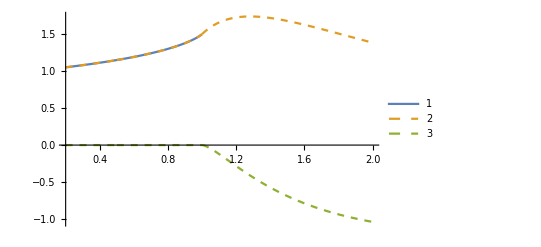

```mathematica
Plot[{fLight2[x],Re[fHeavy2[x]],Im[fHeavy2[x]]},{x,0.2,2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dashed}]
```

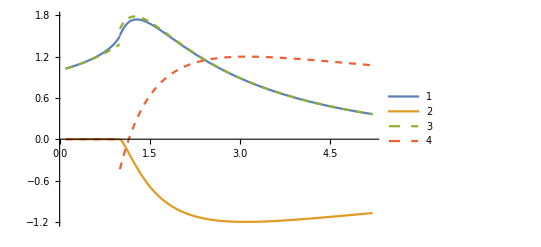

```mathematica
Plot[{Re[fAll2[x]],Im[fAll2[x]],Re[fAll[x]],Im[fAll[x]]},{x,0.1,5.2},PlotLegends->Automatic,PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

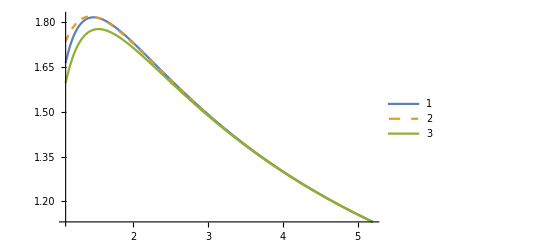

```mathematica
Plot[{Abs[fAll2[x]],Abs[fAll[x]],fHeavyAbs[x]},{x,1.1,5.2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed}]
```

```mathematica
InputForm[Expand[fLight[x]]]
```

1 + (7*x)/30 + (2*x^2)/21 + (26*x^3)/525

```mathematica
InputForm[Expand[fHeavy[x]]]
```

-3/(32*x^3) + (((15*I)/64)*Pi)/x^3 - (((3*I)/8)*Pi)/x^2 - (3*Pi^2)/(8*x^2) + 3/(2*x) + (3*Pi^2)/(8*x) - (15*Log[4*x])/(64*x^3) + (3*Log[4*x])/(8*x^2) - (((3*I)/4)*Pi*Log[4*x])/x^2 + (((3*I)/4)*Pi*Log[4*x])/x + 
 (3*Log[4*x]^2)/(8*x^2) - (3*Log[4*x]^2)/(8*x)

```mathematica
FullSimplify[Expand[fHeavy[x] (Conjugate[fHeavy[x]])],Assumptions->{x>1}]
```

(9 (-2+8 π^2 (-1+x) x+32 x^2+ⅈ π (-5+8 x)+Log[4 x] (-5+8 (1-2 ⅈ π (-1+x)) x-8 (-1+x) x Log[4 x])) (-2+5 ⅈ π-8 π (ⅈ+π) x+8 (4+π^2) x^2+Log[4 x] (-5+8 (1+2 ⅈ π (-1+x)) x-8 (-1+x) x Log[4 x])))/(4096 x^6)

```mathematica
Expand[%]
```

9/(1024 x^6)+(225 π^2)/(4096 x^6)-(27 π^2)/(256 x^5)-9/(32 x^4)+(9 π^2)/(128 x^4)+(9 π^4)/(64 x^4)-(9 π^2)/(8 x^3)-(9 π^4)/(32 x^3)+9/(4 x^2)+(9 π^2)/(8 x^2)+(9 π^4)/(64 x^2)+(45 Log[4 x])/(1024 x^6)-(9 Log[4 x])/(128 x^5)-(45 π^2 Log[4 x])/(256 x^5)-(45 Log[4 x])/(64 x^4)+(117 π^2 Log[4 x])/(256 x^4)+(9 Log[4 x])/(8 x^3)-(9 π^2 Log[4 x])/(32 x^3)+(225 Log[4 x]^2)/(4096 x^6)-(63 Log[4 x]^2)/(256 x^5)+(27 Log[4 x]^2)/(128 x^4)+(9 π^2 Log[4 x]^2)/(32 x^4)+(9 Log[4 x]^2)/(8 x^3)-(9 π^2 Log[4 x]^2)/(16 x^3)-(9 Log[4 x]^2)/(8 x^2)+(9 π^2 Log[4 x]^2)/(32 x^2)-(45 Log[4 x]^3)/(256 x^5)+(117 Log[4 x]^3)/(256 x^4)-(9 Log[4 x]^3)/(32 x^3)+(9 Log[4 x]^4)/(64 x^4)-(9 Log[4 x]^4)/(32 x^3)+(9 Log[4 x]^4)/(64 x^2)

```mathematica
FullSimplify[%,Assumptions->{x>1}]
```

1/(11838003609600 x^16)(1664719257600 π^4 (-1+x)^2 x^12+49 (2840+x (4003+120 x (49+2 x (37+48 x (1-4 x+64 x^3)))))^2+144 π^2 (2722500+7 x (1178100+x (2832543+8 x (821103+x (2045751+10 x (669126+x (-300701+224 x (1163+x (1877+120 x (25+2 x (11+48 x (-5+4 x (1+16 (-1+x) x)))))))))))))+24 Log[4 x] (1650+7 x (357+4 x (147+5 x (55+32 x (4+3 (5-8 x) x))))+107520 (-1+x) x^6 Log[4 x]) (6 (1650+7 x (357+4 x (147+5 x (55+32 x (4+3 (5-8 x) x))))) Log[4 x]+7 (-2840+x (-4003+120 x (-49+2 x (-37+48 x (-1+4 x (1+2 x (2 π^2 (-1+x)-8 x+(-1+x) Log[4]^2))))))+92160 (-1+x) x^6 Log[x] Log[16 x])))

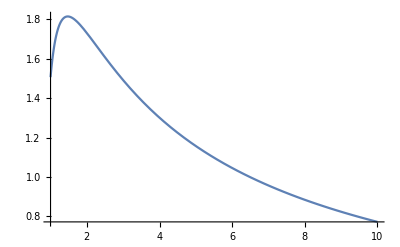

```mathematica
Plot[√(%36),{x,1.,10.}]
```

```mathematica
fHeavy[1.0]
```

1.50475-0.0705083 ⅈ

```mathematica
fHeavy[x]
```

1/(3440640 x^8)(1290240 π^2 (-1+x) x^6+7 (2840+x (4003+120 x (49+2 x (37+48 x (1-4 x+64 x^3)))))-12 ⅈ π (-1650+7 x (-357+4 x (-147+5 x (-55+32 x (-4+3 x (-5+8 x))))))+12 Log[4 x] (-1650+7 x (-357+4 x (-147+5 x (-55+32 x (-4+3 x (-5+8 (1+2 ⅈ π (-1+x)) x)))))-107520 (-1+x) x^6 Log[4 x]))

```mathematica
Expand[%]
```

71/(12288 x^8)+(165 ⅈ π)/(28672 x^8)+4003/(491520 x^7)+(357 ⅈ π)/(40960 x^7)+49/(4096 x^6)+(147 ⅈ π)/(10240 x^6)+37/(2048 x^5)+(55 ⅈ π)/(2048 x^5)+3/(128 x^4)+(ⅈ π)/(16 x^4)-3/(32 x^3)+(15 ⅈ π)/(64 x^3)-(3 ⅈ π)/(8 x^2)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)-(3 ⅈ π Log[4 x])/(4 x^2)+(3 ⅈ π Log[4 x])/(4 x)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)

```mathematica
Re[%]
```

-(165 π Im[1/x^8])/28672-(357 π Im[1/x^7])/40960-(147 π Im[1/x^6])/10240-(55 π Im[1/x^5])/2048-1/16 π Im[1/x^4]-15/64 π Im[1/x^3]+3/8 π Im[1/x^2]+3/4 π Im[Log[4 x]/x^2]-3/4 π Im[Log[4 x]/x]+Re[71/(12288 x^8)+4003/(491520 x^7)+49/(4096 x^6)+37/(2048 x^5)+3/(128 x^4)-3/(32 x^3)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)]

```mathematica
Simplify[%,Assumptions->{x>0}]
```

(7 (2840+4003 x+5880 x^2+8880 x^3+11520 x^4-46080 x^5-184320 π^2 x^6+184320 (4+π^2) x^7)+12 (-1650-2499 x-4116 x^2-7700 x^3-17920 x^4-67200 x^5+107520 x^6) Log[4 x]-1290240 (-1+x) x^6 Log[4 x]^2)/(3440640 x^8)

```mathematica
Expand[%]
```

71/(12288 x^8)+4003/(491520 x^7)+49/(4096 x^6)+37/(2048 x^5)+3/(128 x^4)-3/(32 x^3)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)